# Define functions for MAD data

### Extract the coordinates: X,Y,Z

```mathematica
Clear[GetXYZ];
GetXYZ[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]],y[[6]],y[[1]]};
f/@x
]
```

### Extract the coordinates: X,Y

```mathematica
Clear[GetXY];
GetXY[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]]};
f/@x
]
```

### Extract the coordinates: Name, s

```mathematica
Clear[GetNameS];
GetNameS[x_]:=Module[
{f},
f[y_]:={y[[1]],y[[2]]};
f/@x
]
```

# Get TFS file. Output from: http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/Linac2-PSB/2014/out/ltltbbi.sur

```mathematica
file=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/Linac2-PSB/2014/out/ltltbbi.sur","Table"];
```

```mathematica
file[[Range[1,9]]]
```

{{@,NAME,%06s,SURVEY},{@,TYPE,%06s,SURVEY},{@,TITLE,%57s,LT-LTB-BI 2014 optics. Protons - 311 MeV/c (E_kin=50 MeV)},{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64},{@,DATE,%08s,04/05/14},{@,TIME,%08s,20.07.48},{*,NAME,S,L,Z,X,Y},{$,%s,%le,%le,%le,%le,%le},{LTLTBBI$START,0.,0.,1924.2827927077257754718,1987.7874781706766498246,0.}}

```mathematica
Length[file]
```

261

```mathematica
XYZ=GetXYZ[file[[Range[9,260]]]];
```

```mathematica
XY=GetXY[file[[Range[9,260]]]];
```

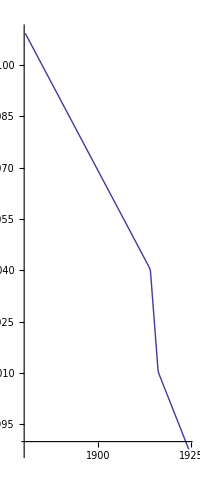

```mathematica
ListLinePlot[XY,AspectRatio->Automatic]
```

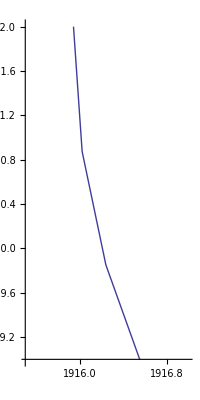

```mathematica
ListLinePlot[XY,AspectRatio->Automatic, PlotRange->{{1915.5,1917},{2009,2012}}]
```

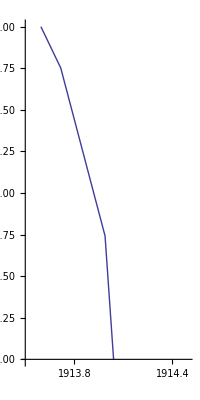

```mathematica
ListLinePlot[XY,AspectRatio->Automatic, PlotRange->{{1913.5,1914.5},{2039,2041}}]
```

# Calculate equations for the straight lines

## LT line - before BHZ20

```mathematica
Clear[x];
GetXYZ[file[[Range[9,62]]]]
XY=GetXY[file[[Range[9,62]]]];
LTlineBeforeBHZ20=LinearModelFit[XY,x,x]
```

{{1924.2827927077257754718,1987.7874781706766498246,0.,LTLTBBI$START},{1924.2827927077257754718,1987.7874781706766498246,0.,LT$START},{1924.2663533288175585767,1987.832575252856258885,0.,DRIFT_0},{1924.2663533288175585767,1987.832575252856258885,0.,LT.VVS10},{1924.1464828576122272352,1988.1614081437492131954,0.,DRIFT_1},{1924.1464828576122272352,1988.1614081437492131954,0.,LT.DHZ10},{1924.1464828576122272352,1988.1614081437492131954,0.,LT.DVT10},{1923.8033108229044501059,1989.1028097342484670662,0.,DRIFT_2},{1923.8033108229044501059,1989.1028097342484670662,0.,LT.BPM10},{1923.6493628891707885487,1989.5251251184095053759,0.,DRIFT_3},{1923.5620286887212841975,1989.7647033674886642984,0.,LT.QFN10},{1923.5474729886464047013,1989.8046330756685620145,0.,DRIFT_4},{1923.5474729886464047013,1989.8046330756685620145,0.,LT.BEC1},{1923.4573988917120459519,1990.0517275051111028006,0.,DRIFT_5},{1923.4573988917120459519,1990.0517275051111028006,0.,LT.BCT10},{1923.3753732407014922501,1990.2767431547363230493,0.,DRIFT_6},{1923.288039040251987899,1990.5163214038154819718,0.,LT.QDN12},{1923.2248501775736713171,1990.6896633134433614032,0.,DRIFT_7},{1923.0515517249168624403,1991.1650617214199883165,0.,LT.BHZ10},{1922.4042511804084369942,1992.9407593322418961179,0.,DRIFT_8},{1922.4042511804084369942,1992.9407593322418961179,0.,LT.VPI11},{1921.7708213618536774447,1994.6784062799747516692,0.,DRIFT_9},{1921.6834871614041730936,1994.9179845290539105918,0.,LT.QFN20},{1921.595296743303151743,1995.1599115844965126598,0.,DRIFT_10},{1921.595296743303151743,1995.1599115844965126598,0.,LT.BEC2},{1921.428334301267113915,1995.6179288253831600741,0.,DRIFT_11},{1921.3410001008176095638,1995.8575070744623189967,0.,LT.QDN22},{1920.2680908861182160763,1998.8007493524635265203,0.,DRIFT_12},{1920.2680908861182160763,1998.8007493524635265203,0.,LT.DHZ20},{1920.2680908861182160763,1998.8007493524635265203,0.,LT.DVT20},{1919.7638471868167471257,2000.1840083960685205966,0.,DRIFT_13},{1919.6765129863672427746,2000.4235866451476795191,0.,LT.QFN30},{1919.4179352556243429717,2001.132926166931156331,0.,DRIFT_14},{1919.3306010551748386206,2001.3725044160103152535,0.,LT.QDN32},{1919.1002785069304081844,2002.0043333277974397788,0.,DRIFT_15},{1919.1002785069304081844,2002.0043333277974397788,0.,LT.VPI2},{1918.3997212245008086029,2003.9261266944304225035,0.,DRIFT_16},{1918.3997212245008086029,2003.9261266944304225035,0.,LT.BPM20},{1918.0214442660831082321,2004.9638293458340285724,0.,DRIFT_17},{1918.0214442660831082321,2004.9638293458340285724,0.,LT.VGP11},{1917.8287952945031520358,2005.4923107776262440893,0.,DRIFT_18},{1917.7414610940536476846,2005.7318890267054030119,0.,LT.QFN40},{1917.486308233916588506,2006.4318333230346524942,0.,DRIFT_19},{1917.3989740334670841548,2006.6714115721138114168,0.,LT.QDN42},{1917.2987965682455069327,2006.9462219166457543906,0.,DRIFT_20},{1917.2987965682455069327,2006.9462219166457543906,0.,LT.DHZ30},{1917.2987965682455069327,2006.9462219166457543906,0.,LT.DVT30},{1917.0922768707118848397,2007.5127540115270221577,0.,DRIFT_21},{1917.0922768707118848397,2007.5127540115270221577,0.,LT.BPM30},{1916.8347266011508054362,2008.2192749656742307707,0.,DRIFT_22},{1916.8347266011508054362,2008.2192749656742307707,0.,LT.CDB10},{1916.5109050853661756264,2009.1075935323578960379,0.,DRIFT_23},{1916.5109050853661756264,2009.1075935323578960379,0.,LT.BCT20},{1916.2397013226441231382,2009.8515692289597609488,0.,DRIFT_24}}

FittedModel[7266.5476870801982425823-2.7432351569706621503687 x]

## LT line - after BHZ20 = Before BHZ30

```mathematica
Clear[x];
GetXYZ[file[[Range[63,111]]]]
XY=GetXY[file[[Range[63,111]]]];
LTlineAfterBHZ20=LinearModelFit[XY,x,x]
```

{{1916.0219121539616935479,2010.8736224946972015459,0.,LT.BHZ20},{1915.9703018844650159736,2011.6061734206382425327,0.,DRIFT_25},{1915.9703018844650159736,2011.6061734206382425327,0.,LT.VGP12},{1915.9107056264122093126,2012.4520766574366916757,0.,DRIFT_26},{1915.9107056264122093126,2012.4520766574366916757,0.,LT.STP10},{1915.6823001562806894071,2015.694040713562799283,0.,DRIFT_27},{1915.6823001562806894071,2015.694040713562799283,0.,LT.BEC3},{1915.602006848703695141,2016.8337157702164859074,0.,DRIFT_28},{1915.5840858041242427134,2017.0880852576972301904,0.,LT.QFN50},{1915.5262816505294267699,2017.9085515457475139556,0.,DRIFT_29},{1915.5262816505294267699,2017.9085515457475139556,0.,LT.VPI14},{1915.4967646359277750889,2018.3275130545391675696,0.,DRIFT_30},{1915.4967646359277750889,2018.3275130545391675696,0.,LT.BEC4},{1915.4713940590916081419,2018.6876204466195758869,0.,DRIFT_31},{1915.4713940590916081419,2018.6876204466195758869,0.,LT.BCT30},{1915.4349194624767278583,2019.2053371681979569985,0.,DRIFT_32},{1915.4349194624767278583,2019.2053371681979569985,0.,LT.DHZ40},{1915.4349194624767278583,2019.2053371681979569985,0.,LT.DVT40},{1915.3533962792912461737,2020.3624689543844397122,0.,DRIFT_33},{1915.3533962792912461737,2020.3624689543844397122,0.,LT.BPM40},{1915.3068367026874057046,2021.0233308581332494214,0.,DRIFT_34},{1915.2889156581079532771,2021.2777003456139937043,0.,LT.QDN55},{1915.2724353249554951617,2021.5116205213560078846,0.,DRIFT_35},{1915.2724353249554951617,2021.5116205213560078846,0.,LT.VVS20},{1914.9645798905212359387,2025.8812893053132029309,0.,DRIFT_36},{1914.9466588459417835111,2026.1356587927939472138,0.,LT.QFN60},{1914.8304883099026483251,2027.7845715881098840328,0.,DRIFT_37},{1914.8125672653231958975,2028.0389410755906283157,0.,LT.QDN65},{1914.7936075029440416984,2028.308054018071061364,0.,DRIFT_38},{1914.765113744848576971,2028.7124915278914158989,0.,LT.BHZ25},{1914.6882092716623446904,2029.8040658132260887214,0.,DRIFT_39},{1914.6882092716623446904,2029.8040658132260887214,0.,LT.VPI25},{1914.5057660099819258903,2032.3936469485195175366,0.,DRIFT_40},{1914.5057660099819258903,2032.3936469485195175366,0.,LT.VPI26},{1914.4770923386545291578,2032.8006381284885719651,0.,DRIFT_41},{1914.4446236225926440966,2033.2614957881594364153,0.,LT.QFW70},{1914.2315740279145757086,2036.2855001069738136721,0.,DRIFT_42},{1914.213652983335123281,2036.539869594454557955,0.,LT.QDN75},{1914.1544432576163217163,2037.3802864305425828206,0.,DRIFT_43},{1914.1544432576163217163,2037.3802864305425828206,0.,LT.DHZ50},{1914.1544432576163217163,2037.3802864305425828206,0.,LT.DVT50},{1914.1098866212892062322,2038.012718803337747886,0.,DRIFT_44},{1914.1098866212892062322,2038.012718803337747886,0.,LT.BCT40},{1914.0755906614663217624,2038.4995121754575393425,0.,DRIFT_45},{1914.0365157564222045039,2039.0541374109056960151,0.,LT.BPM50},{1913.9880431258791304572,2039.742153008061222863,0.,DRIFT_46},{1913.9880431258791304572,2039.742153008061222863,0.,ENDLT},{1913.9880431258791304572,2039.742153008061222863,0.,LT$END},{1913.9880418642726453982,2039.7421709151744835253,0.,DRIFT_47}}

FittedModel[29206.694135797138718593-14.193898483514381727466 x]

## LT line - after BHZ30

```mathematica
Clear[x];
GetXYZ[file[[Range[113,171]]]]
XY=GetXY[file[[Range[113,171]]]];
PlotAfterBHZ30=ListLinePlot[XY];
LTlineAfterBHZ30=LinearModelFit[XY,x,x]
```

{{1913.7170587806213006843,2040.7514246832504341001,0.,LT.BHZ30},{1913.6488468669456324278,2040.8911020419843680429,0.,DRIFT_48},{1913.6488468669456324278,2040.8911020419843680429,0.,LTB.DHZ10},{1913.6488468669456324278,2040.8911020419843680429,0.,LTB.DVT10},{1913.4147354689730491373,2041.3704913444717021775,0.,DRIFT_49},{1913.4147354689730491373,2041.3704913444717021775,0.,LTB.STP10},{1913.2451308666929890023,2041.7177902487103438034,0.,DRIFT_50},{1913.2451308666929890023,2041.7177902487103438034,0.,LTB.VVS10},{1913.0268170513388668041,2042.1648308822389026318,0.,DRIFT_51},{1913.0268170513388668041,2042.1648308822389026318,0.,LTB.VPI11},{1912.3532256813518870331,2043.5441421836785593769,0.,DRIFT_52},{1912.2413261378035258531,2043.773278588803805178,0.,LTB.QFN10},{1911.914403941946602572,2044.442716321424313719,0.,DRIFT_19},{1911.802504398398241392,2044.6718527265495595202,0.,LTB.QDN20},{1911.6662502483129628672,2044.9508599963196502358,0.,DRIFT_53},{1911.6662502483129628672,2044.9508599963196502358,0.,LTB.MSF30},{1911.3557838676838400716,2045.5866011987748152023,0.,DRIFT_54},{1911.3557838676838400716,2045.5866011987748152023,0.,LTB.BPM10},{1911.1945168784525321826,2045.9168271943963191006,0.,DRIFT_55},{1911.1945168784525321826,2045.9168271943963191006,0.,LTB.BCT49},{1911.0466339522729413147,2046.2196466788166162587,0.,DRIFT_56},{1911.0466339522729413147,2046.2196466788166162587,0.,LTB.DHZ20},{1911.0466339522729413147,2046.2196466788166162587,0.,LTB.DVT20},{1909.7613250775552842242,2048.8515703282737376867,0.,DRIFT_57},{1909.7613250775552842242,2048.8515703282737376867,0.,LTB.BCT50},{1909.5375259904585618642,2049.309843138524229289,0.,DRIFT_58},{1909.5375259904585618642,2049.309843138524229289,0.,LTB.BCT55},{1908.1942926461395018123,2052.0603785741636784223,0.,DRIFT_59},{1908.1942926461395018123,2052.0603785741636784223,0.,LTB.BPM20},{1907.9748817764368595817,2052.5096656430364419066,0.,DRIFT_60},{1907.9748817764368595817,2052.5096656430364419066,0.,LTB.DHZ30},{1907.9748817764368595817,2052.5096656430364419066,0.,LTB.DVT30},{1907.6810906219050139043,2053.1112610282571040443,0.,DRIFT_61},{1907.4787938000392841786,2053.5255037057577283122,0.,LTB.QFW30},{1907.2422688824999568169,2054.0098351660026310128,0.,DRIFT_62},{1907.0399720606342270912,2054.4240778435032552807,0.,LTB.QDW40},{1905.0001092050094939623,2058.601099722814069537,0.,DRIFT_63},{1905.0001092050094939623,2058.601099722814069537,0.,LTB.BCT59},{1904.7618290005125345488,2059.0890254796099725354,0.,DRIFT_64},{1904.7618290005125345488,2059.0890254796099725354,0.,LTB.VPI12},{1904.5643592177802929655,2059.4933838415954596712,0.,DRIFT_65},{1904.5643592177802929655,2059.4933838415954596712,0.,LTB.VGR01},{1903.6577535041692499362,2061.3498380101782458951,0.,DRIFT_66},{1903.6577535041692499362,2061.3498380101782458951,0.,LTB.VPI13},{1903.425177982284594691,2061.8260823031832842389,0.,DRIFT_67},{1903.425177982284594691,2061.8260823031832842389,0.,LTB.MSF40},{1903.2356069908614699671,2062.2142663306894974085,0.,DRIFT_68},{1903.2356069908614699671,2062.2142663306894974085,0.,LTB.BCT60},{1903.0515212711809454049,2062.5912181814737778041,0.,DRIFT_69},{1902.8492244493152156792,2063.0054608589744020719,0.,LTB.QFW50},{1902.4810530099543939286,2063.7593645605429628631,0.,DRIFT_70},{1902.278756188088664203,2064.173607238043587131,0.,LTB.QDW60},{1902.0946704684081396408,2064.5505590888278675266,0.,DRIFT_69},{1902.0946704684081396408,2064.5505590888278675266,0.,LTB.DHZ40},{1902.0946704684081396408,2064.5505590888278675266,0.,LTB.DVT40},{1901.8735043117478653585,2065.0034404542516313086,0.,DRIFT_71},{1901.8735043117478653585,2065.0034404542516313086,0.,LTB.BPM30},{1901.5830043202615797782,2065.5982965334392247314,0.,DRIFT_72},{1901.5830043202615797782,2065.5982965334392247314,0.,ENDLTB}}

FittedModel[5959.4648829409053111361-2.0476974066137934346469 x]

# Deflection point for BHZ20

## Crossing Before BHZ20 and After BHZ20

```mathematica
Clear[x,y];

a1=LTlineBeforeBHZ20[[1,2,2]];
b1=LTlineBeforeBHZ20[[1,2,1]];
a2=LTlineAfterBHZ20[[1,2,2]];
b2=LTlineAfterBHZ20[[1,2,1]];
crossBHZ20=Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]  (*  BHZ20 crossing  *)
```

{x→1916.058993530759729749,y→2010.3472931967956416518}

Length from START to deflection point of BHZ20

```mathematica
GetXYZ[file[[Range[9,9]]]]
LengthBeforeBHZ20 = √((crossBHZ20[[1,2]]-GetXYZ[file[[Range[9,9]]]][[1,1]])^2+(crossBHZ20[[2,2]]-GetXYZ[file[[Range[9,9]]]][[1,2]])^2)
```

{{1924.2827927077257754718,1987.7874781706766498246,0.,LTLTBBI$START}}

24.011999644256445368

# Deflection point for BHZ30

```mathematica
Clear[x,y];

a1=LTlineAfterBHZ20[[1,2,2]];
b1=LTlineAfterBHZ20[[1,2,1]];
a2=LTlineAfterBHZ30[[1,2,2]]
b2=LTlineAfterBHZ30[[1,2,1]]
crossBHZ30=Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}] [[1]] (*  BHZ30 crossing  *)
```

-2.0476974066137934346469

5959.4648829409053111361

{x→1913.950634084871778667,y→2040.2731331384878526776}

Length from deflection point of BHZ20 to deflection point of BHZ30

```mathematica
GetXYZ[file[[Range[94,94]]]]
LengthBeforeBHZ20 = √((crossBHZ20[[1,2]]-crossBHZ30[[1,2]])^2+(crossBHZ20[[2,2]]-crossBHZ30[[2,2]])^2)
```

{{1914.6882092716623446904,2029.8040658132260887214,0.,LT.VPI25}}

30.0000179294754059707

# Deflection point for BHZ40 = middle point of BHZ40

```mathematica
Clear[x];
GetXYZ[file[[Range[173,174]]]]
XY=GetXY[file[[Range[173,174]]]];
```

{{1901.5830043202615797782,2065.5982965334392247314,0.,BI1$START},{1901.5830043202615797782,2065.5982965334392247314,0.,BEGBI}}

```mathematica
crossBHZ40={(XY[[1,1]]+XY[[2,1]])/2,(XY[[1,2]]+XY[[2,2]])/2}
```

{1901.5830043202615797782,2065.5982965334392247314}

Length from deflection point of BHZ30 to deflection point of BHZ40

```mathematica
LengthBeforeBHZ20 = √((crossBHZ30[[1,2]]-crossBHZ40[[1]])^2+(crossBHZ30[[2,2]]-crossBHZ40[[2]])^2)
```

28.183721666512693338

# End of BI line

```mathematica
Clear[x];
GetXYZ[file[[Range[260,260]]]]
XY=GetXY[file[[Range[260,260]]]];
```

{{1880.2987457302199345577,2109.1820176499677472748,-0.7199999989811884937,BI1$END}}

```mathematica
crossENDBI={XY[[1,1]],XY[[1,2]]}
```

{1880.2987457302199345577,2109.1820176499677472748}

Length from deflection point of BHZ40 to end of BI line

```mathematica
LengthBeforeBHZ20 = √((crossBHZ40[[1]]-crossENDBI[[1]])^2+(crossBHZ40[[2]]-crossENDBI[[2]])^2)
```

48.5031999984650065058

```mathematica
Sqrt[(1901.350011504084-1880.065749810001)^2+(2066.075410734524-2109.659132211994)^2]
```

48.5032

# Generation of sequence file

```mathematica
NameS[[3,1]]
```

DRIFT_0

```mathematica
If[StringFreeQ[NameS[[3,1]],"OLAV"],1,0]
```

1

```mathematica
Clear[x];
NameS=GetNameS[file[[Range[9,261]]]];  (* 261 *)
For[i=2,i<105,i++,
{
If[StringFreeQ[NameS[[i,1]],"DRIFT"],Print[{NameS[[i,1]],N[(NameS[[i-1,2]]+NameS[[i,2]])/2,11]}]]
}
]
```

{LT$START,0.}

{LT.VVS10,0.048}

{LT.DHZ10,0.398}

{LT.DVT10,0.398}

{LT.BPM10,1.4}

{LT.QFN10,1.977}

{LT.BEC1,2.147}

{LT.BCT10,2.41}

{LT.QDN12,2.777}

{LT.BHZ10,3.342}

{LT.VPI11,5.485}

{LT.QFN20,7.462}

{LT.BEC2,7.847}

{LT.QDN22,8.462}

{LT.DHZ20,11.7222}

{LT.DVT20,11.7222}

{LT.QFN30,13.322}

{LT.QDN32,14.332}

{LT.VPI2,15.132}

{LT.BPM20,17.1775}

{LT.VGP11,18.282}

{LT.QFN40,18.972}

{LT.QDN42,19.972}

{LT.DHZ30,20.392}

{LT.DVT30,20.392}

{LT.BPM30,20.995}

{LT.CDB10,21.747}

{LT.BCT20,22.6925}

{LT.BHZ20,24.008567}

{LT.VGP12,25.267135}

{LT.STP10,26.115135}

{LT.BEC3,29.365135}

{LT.QFN50,30.635135}

{LT.VPI14,31.585135}

{LT.BEC4,32.005135}

{LT.BCT30,32.366135}

{LT.DHZ40,32.885135}

{LT.DVT40,32.885135}

{LT.BPM40,34.045135}

{LT.QDN55,34.835135}

{LT.VVS20,35.197135}

{LT.QFN60,39.705135}

{LT.QDN65,41.613135}

{LT.BHZ25,42.213135}

{LT.VPI25,43.510135}

{LT.VPI26,46.106135}

{LT.QFW70,46.745135}

{LT.QDN75,50.135135}

{LT.DHZ50,51.105135}

{LT.DVT50,51.105135}

{LT.BCT40,51.739135}

{LT.BPM50,52.505135}

{ENDLT,53.472856}

{LT$END,53.472856}

{LTB$START,53.472873952}